Project plots

```mathematica
PacletDirectoryLoad["C:/Users/karlc/Documents/MathematicaPackages/KerrGeodesics"]
<<KerrGeodesics`
SetDirectory[NotebookDirectory[]]
```

{C:\Users\karlc\Documents\MathematicaPackages\KerrGeodesics}

C:\Users\karlc\Documents\College\ACM-Stage4\Stage 4 Research Project\Thesis\images

## Symmetry plot

```mathematica
f[M_,r_]:=1-(2 M)/r;
```

```mathematica
OrbitalSolve[r0_,ϕ0_,E0_,M0_,L0_]:=First@NDSolve[{ϕ'[τ]-L0/r[τ]^2==0,ϕ[0]==ϕ0,3 L0^2-L0^2 r[τ]+r[τ]^2+r[τ]^4 r''[τ]==0,r[0]==r0,r'[0]^2==E0^2-f[M0,r0](1+L0^2/r0^2)},{r,ϕ},{τ,0,1000}];
```

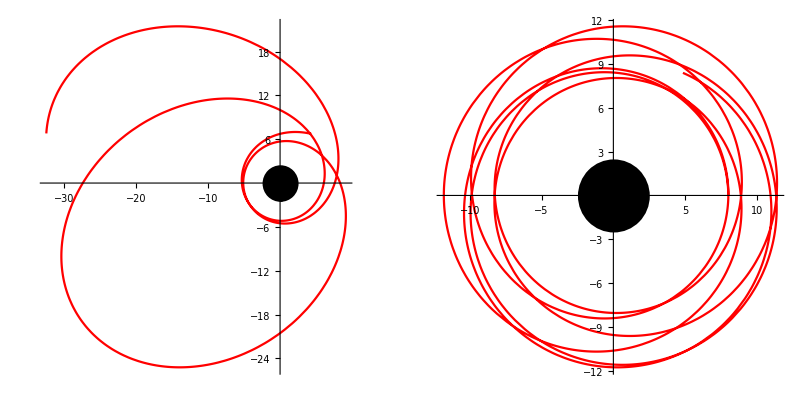

```mathematica
With[{M0=1,r0=8},
E0=0.976;
L0=3.842;
{RSolELMatch,ASolELMatch}=OrbitalSolve[r0,1,E0,1,L0];
nonEcPlot=Show[ParametricPlot[{RSolELMatch[[2]][τ] Cos[ASolELMatch[[2]][τ]],RSolELMatch[[2]][τ] Sin[ASolELMatch[[2]][τ]]},{τ,0,1000}, PlotStyle->Red, TicksStyle->Directive["Label", 14], AxesStyle->Directive[Black,Thickness[0.006]]],Graphics[Disk[{0,0},2.5]]];
E0=0.956;
L0=3.74;
{RSolELMatch,ASolELMatch}=OrbitalSolve[r0,0,E0,1,L0];
ecPlot=Show[ParametricPlot[{RSolELMatch[[2]][τ] Cos[ASolELMatch[[2]][τ]],RSolELMatch[[2]][τ] Sin[ASolELMatch[[2]][τ]]},{τ,0,1000}, PlotStyle->Red,TicksStyle->Directive["Label", 14], AxesStyle->Directive[Black,Thickness[0.005]]],Graphics[Disk[{0,0},2.5]]];
symmetryexample=GraphicsRow[{nonEcPlot,ecPlot}]]
```

```mathematica
Export["schwarzSymmetry.pdf", symmetryexample]
```

schwarzSymmetry.pdf

## Matched orbits figure

```mathematica
OrbitalSolve[r0_,ϕ0_,E0_,M0_,L0_]:=First@NDSolve[{ϕ'[τ]-L0/r[τ]^2==0,ϕ[0]==ϕ0,3 L0^2-L0^2 r[τ]+r[τ]^2+r[τ]^4 r''[τ]==0,r[0]==r0,r'[0]^2==E0^2-f[M0,r0](1+L0^2/r0^2)},{r,ϕ},{τ,0,1000}];
```

```mathematica
f[M_,r_]:=1-(2 M)/r;
With[{E0=Sqrt[217/237],L0=72/Sqrt[395],M0=1,r0=7.2},
Γ[i_,k_,l_]:=1/2 Sum[invg[[i,m]](dg[[l,m,k]]+dg[[k,m,l]]-dg[[m,k,l]]),{m,1,4}];

{RSolELMatch,ASolELMatch}=OrbitalSolve[r0,0,E0,1,L0];

g={{-f[r],0,0,0},{0,f[r]^-1,0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}};
invg=Inverse[g];
dg=Table[D[g,x],{x,{t,r,θ,ϕ}}];

Equations=Table[x[α]''[λ]+Sum[Γ[α,β,δ] x[β]'[λ] x[δ]'[λ],{β,1,4},{δ,1,4}]==0,{α,1,4}]/.{f->Function[{r},1-2M/r]}/.{r->x[2][λ],θ->x[3][λ]}/.{x[3][λ]->π/2,x[3]'[λ]->0,x[3]''[λ]->0};

OutMatch=Block[{M=M0},
First@
NDSolve[Join[Equations[[{1,2,4}]],{x[1][0]==0,x[2][0]==r0,x[4][0]==0,x[1]'[0]==-E0/f[M0,r0],x[4]'[0]==L0/r0^2,x[2]'[0]==-Sqrt[E0^2-f[M0,r0](1+L0^2/r0^2)]}],{x[1],x[2],x[4]},{λ,0,1000}]];];
```

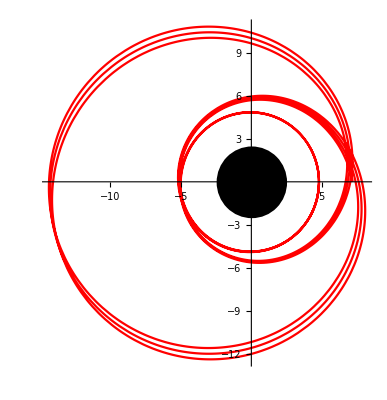

```mathematica
OrbMatchPlotEL=Show[ParametricPlot[{RSolELMatch[[2]][τ] Cos[ASolELMatch[[2]][τ]],RSolELMatch[[2]][τ] Sin[ASolELMatch[[2]][τ]]},{τ,0,1000}, PlotStyle->Red, AxesStyle->Directive[Black,Thickness[0.005]]],Graphics[Disk[{0,0},2.5]]];
radialerror=Plot[{RSolELMatch[[2]][τ] -x[2][τ]/.OutMatch},{τ,0,1000},GridLines->Automatic,Frame->True,FrameLabel->{"τ","Radial Error"},ImagePadding->{{Automatic,20},{Automatic,Automatic}}];
angularerror=Plot[{ASolELMatch[[2]][τ] -x[4][τ]/.OutMatch},{τ,0,1000},GridLines->Automatic,Frame->True,FrameLabel->{"τ","Angular Error"}];
matchedorbits=GraphicsRow[{OrbMatchPlotEL,GraphicsColumn[{radialerror,angularerror},Spacings->0]}]
```

```mathematica
Export["MatchedOrbits.pdf",matchedorbits]
```

MatchedOrbits.pdf

## Potential Energy Graph

```mathematica
VLr[L_,r_,M_]:=(1-2M/r)(1+L^2/r^2)
```

```mathematica
With[{M=1,L=3.9},rmax=FindRoot[D[VLr[3.9,r/3,1],r]==0,{r,10}];
vmax=VLr[L,r/3,M]/.rmax]
```

0.975642

```mathematica
With[{M=1,L=3.9},rmin=FindRoot[D[VLr[3.9,r/3,1],r]==0,{r,40}];
vmin=VLr[L,r/3,M]/.rmin]
```

0.921025

```mathematica
line1=Line[{{9.788709362260839,0},{9.788709362260839,0.94}}];
line2=Line[{{19.885190428465002,0},{19.885190428465002,0.94}}];
line3=Line[{{70.32610020927416,0},{70.32610020927416,0.94}}];
```

```mathematica
eUnstableTxt=Text[Style["E_Unstable",14],Scaled[{0.42,0.9}],{0,0},Background->White];
eBoundTxt=Text[Style["E_Bound",14],Scaled[{0.42,0.5}],{0,0},Background->White];
eStableTxt=Text[Style["E_Stable",14],Scaled[{0.42,0.3}],{0,0},Background->White];
r1Txt=Text[Style["r_1",14],Scaled[{0.1,0.385}],{0,0},Background->White];
r2Txt=Text[Style["r_2",14],Scaled[{0.22,0.385}],{0,0},Background->White];
r3Txt=Text[Style["r_3",14],Scaled[{0.895,0.385}],{0,0},Background->White];
txt=Graphics[{eUnstableTxt,eBoundTxt,eStableTxt,r1Txt,r2Txt,r3Txt}];
```

```mathematica
(* ticks = {{{9.788709362260839,"r_3"},{19.885190428465002,"r_1"},{70.32610020927416,"r_2"}},{{0.94,"E^2"}}} *)
```

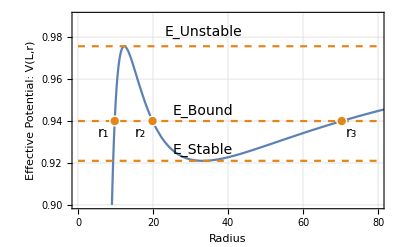

```mathematica
radialPE=Show[{Plot[VLr[3.9,r/3,1],{r,2,200},PlotRange->{{0,80},{0.9,0.99}},FrameLabel->{"Radius","Effective Potential: V(L,r)"},LabelStyle->Directive[12],Frame->True,GridLines->Automatic],
Plot[{0.94},{r,0,80},PlotStyle->{Dashed,ColorData[98,"ColorList"][[2]]}],
Plot[{vmax},{r,0,80},PlotStyle->{Dashed,ColorData[98,"ColorList"][[2]]}],
Plot[{vmin},{r,0,80},PlotStyle->{Dashed,ColorData[98,"ColorList"][[2]]}],
Graphics[{PointSize[0.02],White,Point[{9.788709362260839,0.94}]}],
Graphics[{PointSize[0.02],White,Point[{70.32610020927416,0.94}]}],
Graphics[{PointSize[0.02],White,Point[{19.885190428465002,0.94}]}],
Graphics[{PointSize[0.015],ColorData[98,"ColorList"][[2]],Point[{9.788709362260839,0.94}]}],
Graphics[{PointSize[0.015],ColorData[98,"ColorList"][[2]],Point[{19.885190428465002,0.94}]}],
Graphics[{PointSize[0.015],ColorData[98,"ColorList"][[2]],Point[{70.32610020927416,0.94}]}]},
txt]
```

```mathematica
Export["RadialPotentialPE.pdf",radialPE]
```

RadialPotentialPE.pdf

```mathematica
ColorData[98,"ColorList"][[2]]
```

RGBColor[0.886243, 0.527215, 0.0910023]

```mathematica
VLr[8,r,1]=.
```

```mathematica
SolveValues[VLr[3.9,r/3,1]==0.94,r]
```

{9.78871,19.8852,70.3261}

```mathematica
VLr[8,2,1]
```

0

## p-e plane

```mathematica
sepTxt=Inset[Rotate[Text[Style["Separatrix",14]],ArcTan[5/2],Center],{7,0.62}];
boundTxt=Text[Style["Allowed (p,e) values\nfor bound motion",14],{9,0.5}];
peTxts=Graphics[{sepTxt,boundTxt}];
```

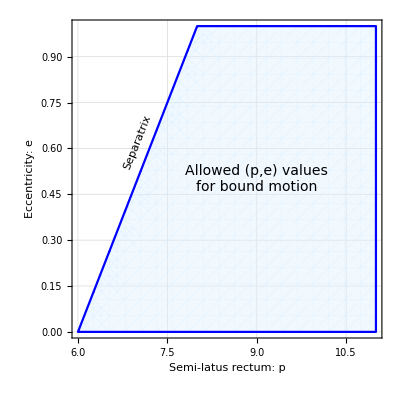

```mathematica
peplane=Show[{RegionPlot[x>6+2y,{x,6,11},{y,0,1},BoundaryStyle->Blue,PlotStyle->Directive[LightBlue,Opacity[0.4]],AxesLabel->{"p","e"}, GridLines->Automatic,FrameLabel->{Style["Semi-latus rectum: p",16],Style["Eccentricity: e",16]},FrameTicksStyle->Directive["Label", 16]],peTxts}]
```

```mathematica
Export["PEPlane.pdf",peplane]
```

PEPlane.pdf

## rθ perturbed and unperturbed

p→8.99834

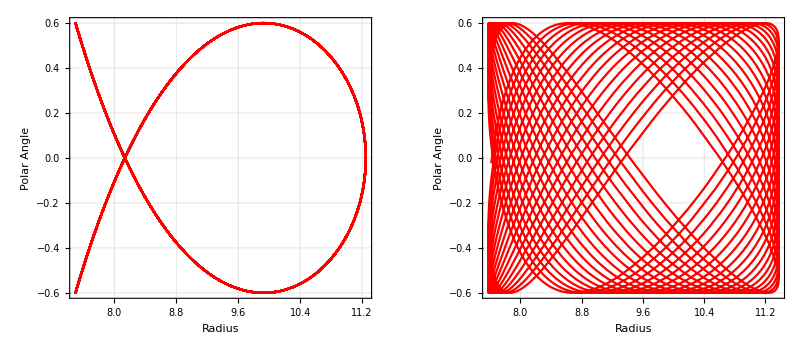

resorThPlusPert.pdf

```mathematica
With[{a=0.4,e=0.2,x=0.8,λmax=50},
pRes=KerrGeoFindResonance[<|"a"->a,"e"->e,"x"->x|>,{2,3,0}];
Print[pRes];
orbit=KerrGeoOrbit[a,pRes[[2]],e,x];
{t,r,θ,ϕ}=orbit["Trajectory"];]
KerrRTh=ParametricPlot[{r[λ],Cos[θ[λ]]},{λ,0,50},PlotStyle->Red,AspectRatio->1,FrameLabel->{Style["Radius",12],Style["Polar\nAngle",12]},GridLines->Automatic,Frame->True,FrameTicksStyle->12];

With[{a=0.4,e=0.2,x=0.8,λmax=50},
orbit=KerrGeoOrbit[a,pRes[[2]]+0.1,e,x];
{t,r,θ,ϕ}=orbit["Trajectory"];]
KerrRThPert=ParametricPlot[{r[λ],Cos[θ[λ]]},{λ,0,50},PlotStyle->Red,AspectRatio->1,FrameLabel->{Style["Radius",12],Style["Polar\nAngle",12]},GridLines->Automatic,Frame->True,FrameTicksStyle->12];
rThPert=GraphicsRow[{KerrRTh,KerrRThPert}]
Export["resorThPlusPert.pdf",rThPert]
```

## p-e resonance surface for specific a,p,e values

```mathematica
PacletDirectoryLoad["C:/Users/karlc/Documents/MathematicaPackages/KerrGeodesics"]
<<KerrGeodesics`
```

{C:\Users\karlc\Documents\MathematicaPackages\KerrGeodesics}

```mathematica
(* p as dependent variable *)
```

```mathematica
APEvalues1=Table[{x,e,(KerrGeoFindResonance[<|"a"->0.9,"x"->x,"e"->e|>,{2,3,0}][[2]])},{x,-0.99,0.99,0.1},{e,0,1,0.1}];//Quiet
flatAPEvalues1=Flatten[APEvalues1,1];
```

```mathematica
pexPlot=ListPlot3D[flatAPEvalues1,AxesLabel->{Style["x",16],Style["e",16],Style["p",16]},ColorFunction->"LakeColors",PlotLegends->Placed[BarLegend[Automatic], Left],ViewPoint->{2.207212695653824,-2.2670035404671607,1.1995445234145903},AxesEdge->{{0,0},{1,0},{1,1}},ImageSize->375,Lighting->AmbientLight[White],TicksStyle->Directive["Label", 12],ImageSize->Small]
```

-Graphics3D-

```mathematica
Export["pexplot.pdf",pexPlot]
```

pexplot.pdf

```mathematica
pro=KerrGeoFrequencies[0.9,p1,0,1,Time->"Mino"];
retro=KerrGeoFrequencies[0.9,p2,0,-1,Time->"Mino"];
```

```mathematica
prop=FindRoot[3"Υ_r"==2"Υ_θ"/.pro,{p1,4}]
retrop=FindRoot[3"Υ_r"==2"Υ_θ"/.retro,{p2,16}]
```

{p1→4.96263}

{p2→15.2677}

```mathematica
newfit=FindFit[{{-1,p2},{1,p1}}/.prop/.retrop,α+β x,{α,β},x]
```

{α→10.1152,β→-5.15252}

```mathematica
PXValuesE01=Table[{x,(KerrGeoFindResonance[<|"a"->0.9,"x"->x,"e"->0|>,{2,3,0}][[2]])},{x,-0.99,0.99,0.05}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

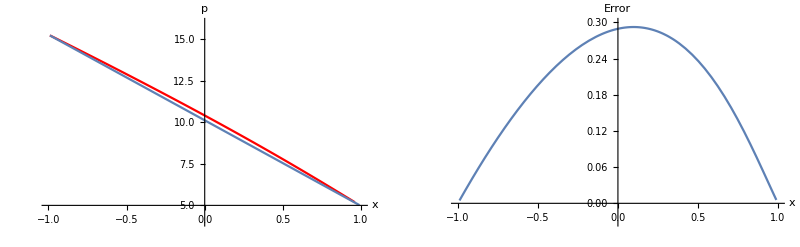

```mathematica
lineFit=GraphicsRow[{Show[{ListLinePlot[PXValuesE01,PlotStyle->Directive[Red]],Plot[α+β x/.newfit,{x,-0.99,0.99}]},AxesLabel->{"x","p"},AxesOrigin->{0,5},PlotRange->{{-1,1},{4,16}}],Plot[{KerrGeoFindResonance[<|"a"->0.9,"x"->x,"e"->0|>,{2,3,0}][[2]]-(α+β x/.newfit)},{x,-0.99,0.99},AxesLabel->{"x","Error"},PlotRange->{{-1,1},{-0.031,0.3}},AxesOrigin->{0,0}]}]
```

```mathematica
Table[{e,x,Abs[(KerrGeoFindResonance[<|"a"->0.9,"x"->x,"e"->e|>,{2,3,0}][[2]])-(α+β x+e)/.newfit]},{x,-0.99,0.99,0.05},{e,0,1,0.1}];//Quiet
pErrVals=Flatten[%,1];
```

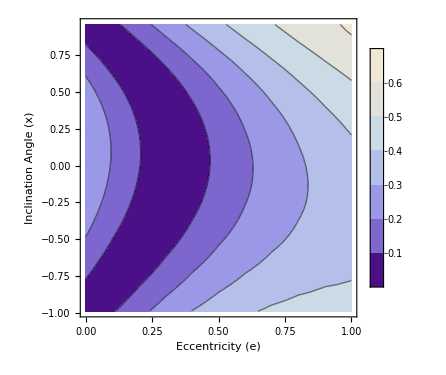

```mathematica
errContour=ListContourPlot[pErrVals,FrameLabel->{Style["Eccentricity (e)",16],Style["Inclination Angle (x)",16]}, PlotLegends->Placed[BarLegend[Automatic,LabelStyle->{FontSize->16}], Right],ColorFunction->"LakeColors",FrameTicksStyle->Directive["Label", 16],ImageSize->375]
```

```mathematica
Export["planeErr.pdf",errContour]
```

planeErr.pdf

```mathematica
planeErr=GraphicsRow[{pexPlot,errContour},ImageSize->900]
```

-Graphics-

```mathematica
Export["planeErr.pdf",planeErr]
```

planeErr.pdf

## Prograde and Retrograde Frequencies plotted with intersection

```mathematica
pro09=KerrGeoFrequencies[0.9,p,0,1,Time->"Mino"]/.Abs->Identity;
retro09=KerrGeoFrequencies[0.9,p,0,-1,Time->"Mino"]/.Abs->Identity;
```

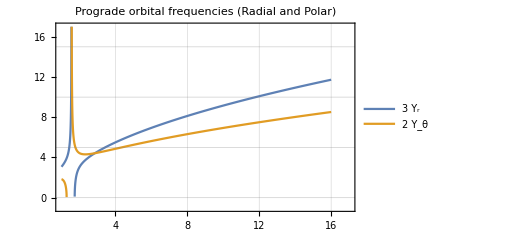

```mathematica
proretfreqplot1=Plot[{3 "Υ_r"/.pro09,2 "Υ_θ"/.pro09},{p,1,16},PlotLabel->"Prograde orbital frequencies (Radial and Polar)",LabelStyle->Directive[12],AxesStyle->Directive[12],PlotRange->{{1,17},{-1,17}},PlotLegends->Placed[LineLegend[{Style["3 Υ_r",12],Style["2 Υ_θ",12]},LegendFunction->(Framed[#1, FrameMargins -> 0,Background->White] & )],{0.8,0.25}],Frame->True,GridLines->{Automatic,{0,5,10,15}},ImageSize->375]
```

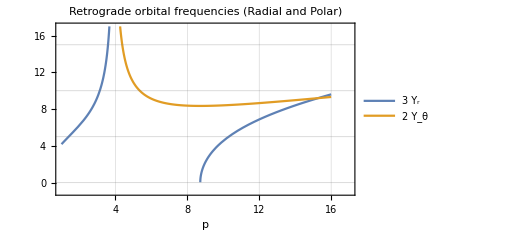

```mathematica
proretfreqplot2=Plot[{3 "Υ_r"/.retro09,2 "Υ_θ"/.retro09},{p,1,16},AxesLabel->{"p"},PlotLabel->"Retrograde orbital frequencies (Radial and Polar)",LabelStyle->Directive[12],AxesStyle->Directive[12],PlotRange->{{1,17},{-1,17}},PlotLegends->Placed[LineLegend[{Style["3 Υ_r",12],Style["2 Υ_θ",12]},LegendFunction->(Framed[#1, FrameMargins -> 0,Background->White] & )],{0.8,0.25}],Frame->True,GridLines->{Automatic,{0,5,10,15}},ImageSize->375]
```

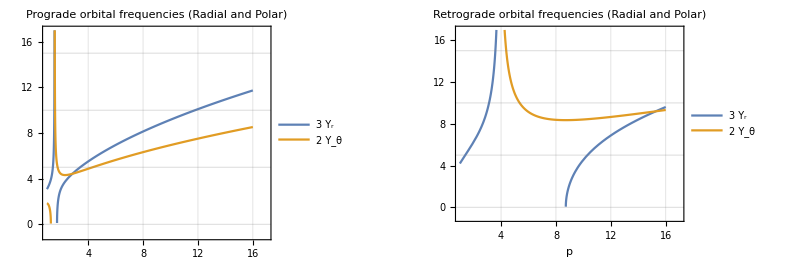

```mathematica
proretfreqplots=GraphicsRow[{proretfreqplot1,proretfreqplot2},ImageSize->Full]
```

```mathematica
Export["proretfreqplots.pdf",proretfreqplots]
```

proretfreqplots.pdf